```mathematica
Needs["VariationalMethods`"]
data=prepareDataSim["/Users/digant/goliath/resources/sho_coupled_0.1_sim.csv", 0.1, 2];
```

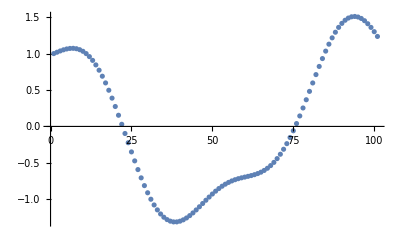

```mathematica
ListPlot[th1/.data[[1]]]
```

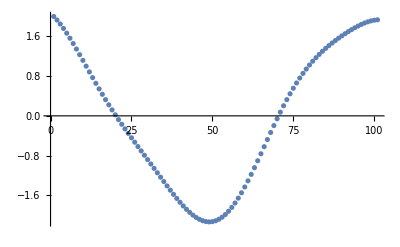

```mathematica
ListPlot[th2/.data[[1]]]
```

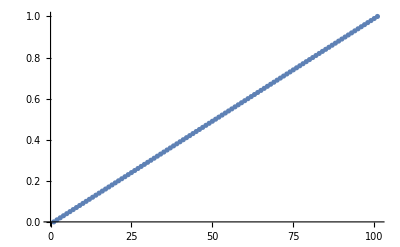

```mathematica
ListPlot[th1/.data[[2]]]
```

```mathematica
ListPlot[th2/.data[[2]]]
```

-Graphics-

```mathematica
vars = {th1, th2}
```

{th1,th2}

```mathematica
indiv =polynomialiser2[ vars,{{0 ,2 ,0, 0},
{2, 0, 0, 0},{0, 0, 2, 0},{0 ,0, 0, 2},{1, 1, 0, 0}, {1, 0, 2,1}, {3, 0, 1, 0}, {0, 2, 0, 1}, {0, 0, 1, 1}}]
```

{{c1,c2,c3,c4,c5,c6,c7,c8,c9},c2 th1^2+c7 th1^3 th1dot+c3 th1dot^2+c5 th1 th2+c1 th2^2+c9 th1dot th2dot+c6 th1 th1dot^2 th2dot+c8 th2^2 th2dot+c4 th2dot^2}

```mathematica
scoreFn = generateScore[vars, indiv⟦2⟧, data⟦1⟧, data⟦2⟧];
```

```mathematica
nmSolve[scoreFn, indiv⟦1⟧, indiv⟦2⟧]
```

{-23.3254,{c1→-0.0641078,c2→-0.0241474,c3→0.0641078,c4→0.168176,c5→-0.0799209,c6→-1.88956×10^-9,c7→0.258295,c8→0.512107,c9→0.208136}}

```mathematica
scoreAndGetCoefficients[{{0 ,2 ,0, 0},
{2, 0, 0, 0},{0, 0, 2, 0},{0 ,0, 0, 2},{1, 1, 0, 0}, {1, 0, 2,1}, {3, 0, 1, 0}, {0, 2, 0, 1}, {0, 0, 1, 1}}, data⟦1⟧, data⟦2⟧, 2]
```

{-23.3254,-0.0641078,-0.0241474,0.0641078,0.168176,-0.0799209,-1.88956×10^-9,0.258295,0.512107,0.208136}

```mathematica
L1[th1_, th2_, th1dot_, th2dot_] := -0.024147369848349563 th1^2+0.2582954398093366 th1^3 th1dot+0.06410780574490355 th1dot^2+-0.07992086912745383 th1 th2+-0.0641078055734092 th2^2+0.2081364835842071 th1dot th2dot+-1.889562603047237*^-9 th1 th1dot^2 th2dot+0.5121071613651865 th2^2 th2dot+0.1681760502462219 th2dot^2
```

```mathematica
sol2=EulerEquations[L1[th1[t], th2[t],  D[th1[t],t], D[th2[t],t] ], {th1[t], th2[t]}, t]
```

{0.-0.0799209 th2[t]+1.88956×10^-9 th1'[t]^2 th2'[t]-0.128216 th1''[t]-0.208136 th2''[t]+th1[t] (-0.0482947+3.77913×10^-9 th2'[t] th1''[t]+3.77913×10^-9 th1'[t] th2''[t])==0,0.-0.128216 th2[t]+1.88956×10^-9 th1'[t]^3-0.208136 th1''[t]+th1[t] (-0.0799209+3.77913×10^-9 th1'[t] th1''[t])-0.336352 th2''[t]==0}

```mathematica
sol3=NDSolve[{sol2, th1[0]==1, th1[1]==1, th2[0]== 2, th2[1]== 1}, {th1[t], th2[t]}, {t,0,300.0}]
```

{{th1[t]→InterpolatingFunction[{{0., 300.}}, <>][t],th2[t]→InterpolatingFunction[{{0., 300.}}, <>][t]}}

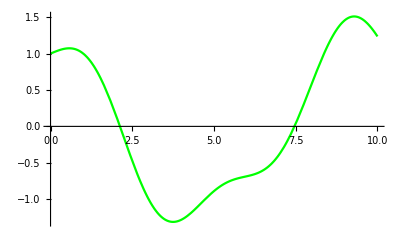

```mathematica
p1 = Plot[Evaluate[th1[t]/.sol3], {t, 0,10.0}, PlotRange->All, PlotStyle -> Green]
```

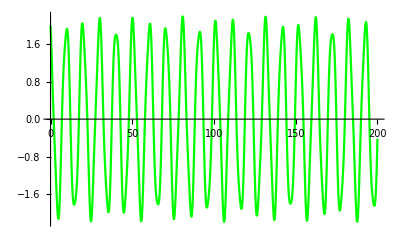

```mathematica
v1 = Plot[Evaluate[th2[t]/.sol3], {t,0,200.0}, PlotRange->All, PlotStyle -> Green]
```

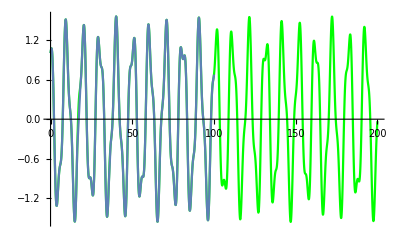

```mathematica
Show[p1, p2]
```

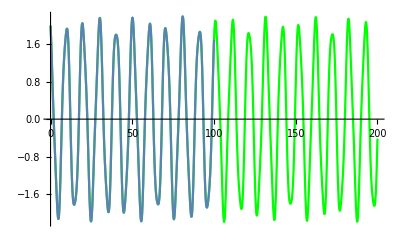

```mathematica
Show[v1, v2]
```